```mathematica
a=Get["/home/drchaj1/java/exp/results/find_cluster_001_001.txt"];
```

```mathematica
MatrixForm[a];
```

```mathematica
Length[a]
```

12

```mathematica
plotSandwich[m_]:=
ArrayPlot[m,ColorRules->{Max[m]->Red},Mesh->True]
```

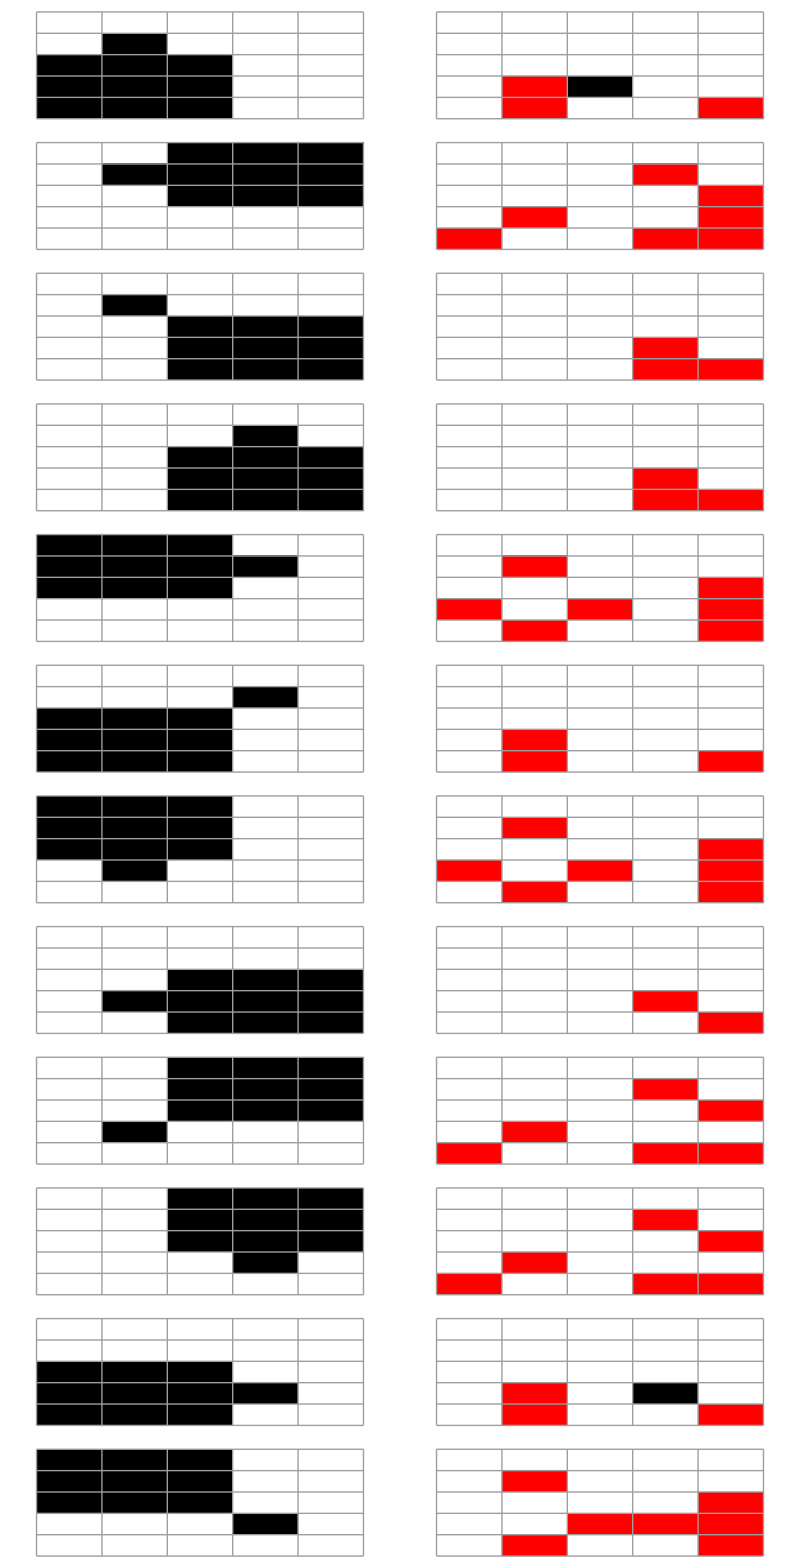

```mathematica
Grid[Partition[Sequence@@{ArrayPlot[#⟦1⟧, Mesh->True], plotSandwich[#⟦2⟧]}&/@a,2]]
```